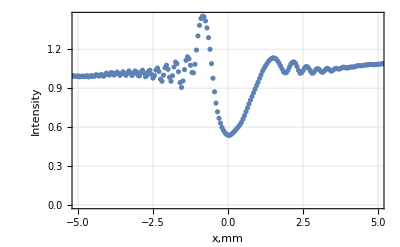

```mathematica
expImage = -Graphics-;
grayImage=ColorConvert[expImage,"Grayscale"];
intensVals=Mean[ImageData[grayImage]];
x=Range[Length[intensVals]];
x=x/20-5.5;
Normi:=intensVals[[1]]+intensVals[[2]]+intensVals[[3]]

Normi = Normi/3;
intensVals=intensVals/Normi;

PlotValues = Transpose[{x,intensVals}];
ListPlot[PlotValues, PlotRange->{{-5,5},Full}, AxesOrigin->{-6,0},FrameLabel->{"x,mm","Intensity"}, GridLines->Automatic, Frame->True]
```